```mathematica
low={#[[2]],#[[1]]}&/@Import["low.csv"];
```

```mathematica
high={#[[2]],#[[1]]}&/@Import["high.csv"];
```

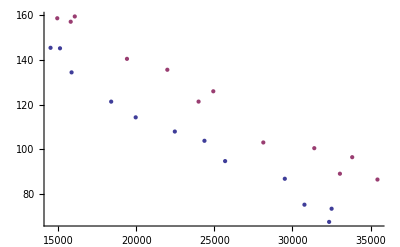

```mathematica
ListPlot[{low,high}]
```

```mathematica
lowF=Fit[low, {1, x},x]
```

199.778-0.00400705 x

```mathematica
highF=Fit[high,{1,x},x]
```

214.151-0.00366614 x

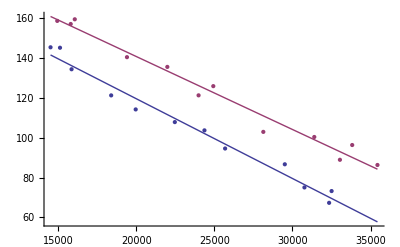

```mathematica
Show[
ListPlot[{low,high}],
Plot[{lowF,highF},{x,Min[low[[All,1]],high[[All,1]]],Max[low[[All,1]],high[[All,1]]]}]]
```

```mathematica
Integrate[a x+b
```